```mathematica
Needs["Constants`"]
Needs["Utilities`"]
Needs["EnergyLoss`"]
```

```mathematica
SIConstRepl
```

{e→1.60289×10^-19,m→9.11×10^-31,hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,α→1/137,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23}

#### Load params

```mathematica
SiO2Totalparams= ReadIt[NotebookDirectory[]<>"../ELandKappamin/extract optical data/SiO2Totalparams"];
MgOTotalparams =ReadIt[NotebookDirectory[]<>"../ELandKappamin/extract optical data/MgOTotalparams"];
FeTotalparams =ReadIt[NotebookDirectory[]<>"../ELandKappamin/extract optical data/FeTotalparams"];
```

```mathematica
"qF"/.SiO2Totalparams
"qF"/.MgOTotalparams
```

{2.2927×10^10,3.90562×10^10}

{1.64516×10^10,2.19692×10^10,2.34828×10^10,3.63218×10^10}

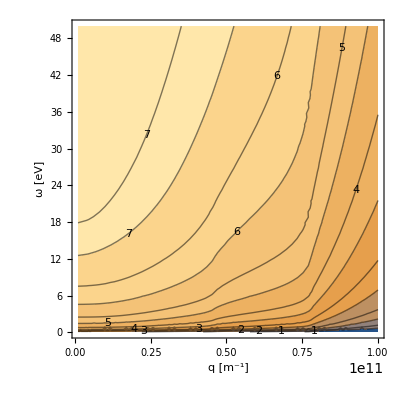

```mathematica
ContourTotalParamsωq[SiO2Totalparams,"SiO2"]
```

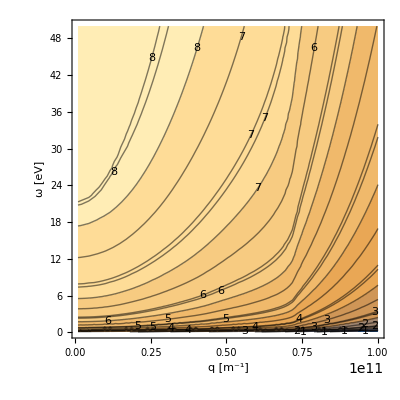

```mathematica
ContourTotalParamsωq[MgOTotalparams,"MgO"]
```

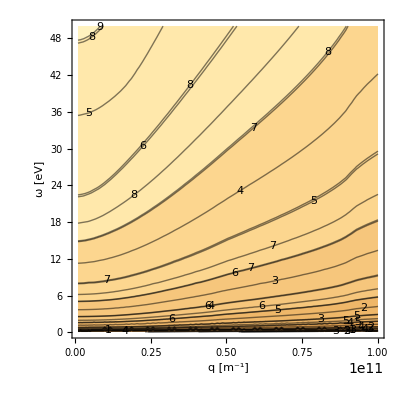

```mathematica
ContourTotalParamsωq[FeTotalparams,"Fe"]
```